```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,1.25},{1.25,1.5}}],{x}]][[1]]
fDerivative[f_,z_]:=Module[{x,v},v=Array[x,Length[z]];
D[f@@v,{v}]/.Thread[v->z]]
fLeapFrogStep[θ_,m_,ϵ_,logP_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[logP,θ];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[logP,θ1];m1=m1+0.5 ϵ grad1;{θ1,m1}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];Cprimed = Union[{Cprimed},{Cprimedprimed}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
fNUTSstep[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};While[s==1,v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1];C]
fNUTSstepExtract[c_]:=Module[{dep=Depth@c},RandomChoice@DeleteCases[Flatten[c,dep-4],{}]]
fNUTSstepComplete[θ_,ϵ_,logP_,Δ_]:=Module[{c=fNUTSstep[θ,ϵ,logP,Δ]},fNUTSstepExtract[c]]
fNUTS[M_Integer,θ0_,ϵ_,logP_,Δ_]:=NestList[fNUTSstepComplete[#[[1]],ϵ,logP,Δ]&,{θ0,{}},M]
```

```mathematica
samples=fNUTS[100,{5,5},0.1,f,1000];
```

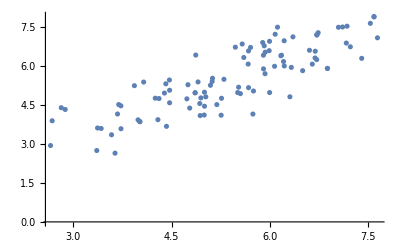

```mathematica
ListPlot[samples[[All,1]]]
```

## Visualising tree

```mathematica
fNUTSstepSingle[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1;C]
fNUTSstepSingleString[thetaMinus_,mMinus_,thetaPlus_,mPlus_,C_,j_,s_,u_,ϵ_,logP_,Δ_]:=Module[{thetaMinus1=thetaMinus,mMinus1=mMinus,thetaPlus1=thetaPlus,mPlus1=mPlus,s1=s,temp1,temp2,Cprimed,sprimed,v,C1,j1,dep},
v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus1,mMinus1,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus1,mMinus1,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus1,mPlus1,Cprimed,sprimed}=fBuildTree[thetaPlus1,mPlus,u,v,j,ϵ,logP,Δ]];
dep=Depth@Cprimed-4;
If[sprimed==1,C1=Join[{C},{Cprimed}]];
s1=sprimed If[(thetaPlus1-thetaMinus1).mMinus1 ≥ 0,1,0]If[(thetaPlus1-thetaMinus1).mPlus1 ≥ 0,1,0];j1 = j + 1;{thetaMinus1, mMinus1, thetaPlus1, mPlus1,C1,j1,s1,u,ϵ,logP,Δ}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{res[[1]],res[[2]],{}}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];
sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];
Cprimed = DeleteCases[Union[{Cprimed},{Cprimedprimed}],{}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
fNUTSstring[theta0_,m0_,u_,ϵ_,logP_,Δ_]:=NestWhileList[fNUTSstepSingleString@@#&,{theta0,m0,theta0,m0,{theta0,m0},0,1,u,ϵ,logP,Δ},#[[7]]==1 &]
fUnravel[lTree__]:=Module[{len=(Length@lTree)-1,lDeps,lAll},lDeps=Table[Depth@lTree[[i]][[5]],{i,1,len,1}];lAll=Table[Flatten[lTree[[i]][[5]],If[lDeps[[i]]-4>0,lDeps[[i]]-4,0]],{i,1,len,1}];Table[If[i==1,{lAll[[i]]},lAll[[i]]],{i,1,len,1}]]
fMaxMins[test__]:=Module[{maxes=Max/@Thread@fUnravel[test][[Length@test-1]][[All,1]],mins=Min/@Thread@fUnravel[test][[Length@test-1]][[All,1]]},Thread[{mins-0.1,maxes+0.1}]]
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,1.25},{1.25,1.5}}],{x}]][[1]]
```

```mathematica
test=fNUTSstring[{5.8,5.3},{0.1,0.2},0.001,0.6,f,1000];
```

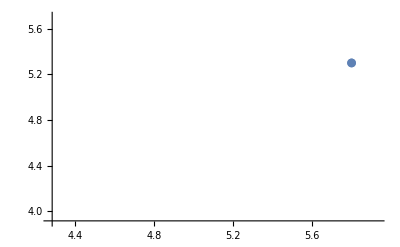
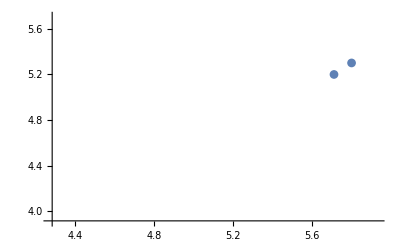
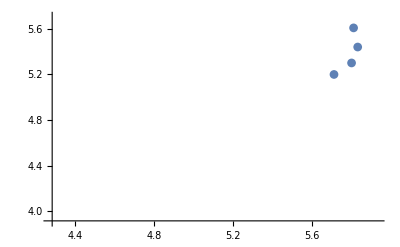
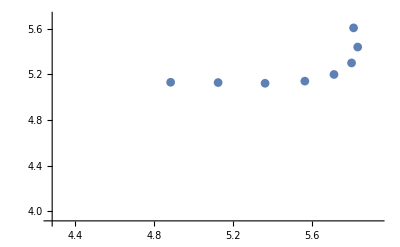
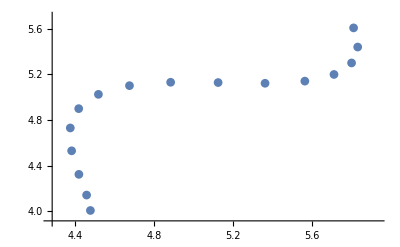

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,1]],PlotMarkers->Automatic,PlotRange->fMaxMins[test]],{i,1,Length@test-1,1}]
```

```mathematica
fDisjoint[test__,posOrm_]:=Table[Complement[fUnravel[test][[i]][[All,posOrm]],Flatten[Union[Table[fUnravel[test][[j]][[All,1]],{j,1,i-1,1}]],1]],{i,1,Length@test-1,1}]
```

```mathematica
c01=RGBColor[58.4/100,38.8/100,23.9/100];
c02=RGBColor[62.4/100,63.5/100,63.1/100];
c03=RGBColor[58.0/100,41.6/100,61.2/100];
c04=RGBColor[84.3/100,36.1/100,33.7/100];
c05=RGBColor[96.1/100,71.8/100,40.8/100];
c06=RGBColor[50.2/100,67.8/100,43.5/100];
c07=RGBColor[29.0/100,50.2/100,67.1/100];
c08=RGBColor[56.1/100,57.3/100,56.9/100];
c09=RGBColor[51.4/100,34.5/100,54.5/100];
c10=RGBColor[81.2/100,27.5/100,23.5/100];
c11=RGBColor[94.9/100,67.8/100,31.0/100];
c12=RGBColor[42.7/100,62.7/100,36.1/100];
c13=RGBColor[18.8/100,43.5/100,61.6/100];
apple13={c01,c02,c03,c04,c05,c06,c07,c08,c09,c10,c11,c12,c13}
```

{RGBColor[0.584, 0.38799999999999996, 0.239],RGBColor[0.624, 0.635, 0.631],RGBColor[0.58, 0.41600000000000004, 0.612],RGBColor[0.843, 0.36100000000000004, 0.337],RGBColor[0.961, 0.718, 0.408],RGBColor[0.502, 0.6779999999999999, 0.435],RGBColor[0.29, 0.502, 0.6709999999999999],RGBColor[0.561, 0.573, 0.569],RGBColor[0.514, 0.34500000000000003, 0.545],RGBColor[0.812, 0.275, 0.23500000000000001],RGBColor[0.9490000000000001, 0.6779999999999999, 0.31],RGBColor[0.42700000000000005, 0.627, 0.36100000000000004],RGBColor[0.188, 0.435, 0.616]}

```mathematica
blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
apple7={blue,green,yellow,Orange,red,purple,grey};
```

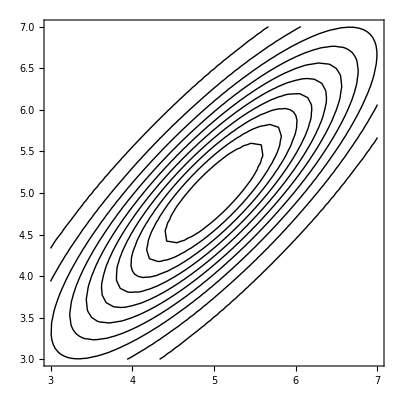

```mathematica
gMain=ContourPlot[Exp[f[{x,y}]],{x,3,7},{y,3,7},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
lAnimations=Table[Show[gMain,Table[ListPlot[fDisjoint[test,1][[i]],PlotRange->fMaxMins[test],PlotStyle->apple13[[i]]],{i,1,j,1}]],{j,1,Length@test-1,1}];
```

```mathematica
ListAnimate[lAnimations]
```

```mathematica
lAnimationsMomentum=Table[Show[Table[ListPlot[fDisjoint[test,2][[i]],PlotRange->{{-1,1},{-1,1}},PlotStyle->apple13[[i]]],{i,1,j,1}]],{j,1,Length@test-1,1}];
```

```mathematica
ListAnimate[lAnimationsMomentum]
```

## Putting momentum arrow and points together == think wrong

```mathematica
fPlotArrow[points__,momenta__,plotRange__,colour_]:=Module[{first=points[[1]],last=points[[-1]],momfinal=momenta[[-1]],momstart=momenta[[1]]},Show[ListPlot[points,PlotRange->plotRange,PlotStyle->colour],Graphics[{Black,Arrow[{first,last}]}],Graphics[{Magenta,Arrow[{last,last+momfinal}]}],Graphics[{Magenta,Arrow[{first,first+momstart}]}]]]
```

```mathematica
ListAnimate[Table[fPlotArrow[fDisjoint[test,1][[i]],fDisjoint[test,2][[i]],{{2,7},{2,7}},Blue],{i,2,5,1}]]
```

## Visualise the elements as U-turn sampler progresses

```mathematica
test=fNUTSstring[{5.8,5.3},{0.1,0.2},0.001,0.6,f,1000];
```

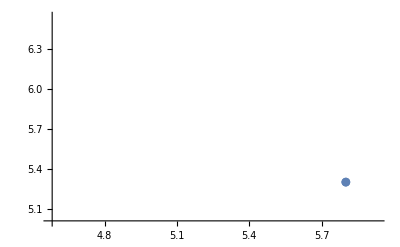
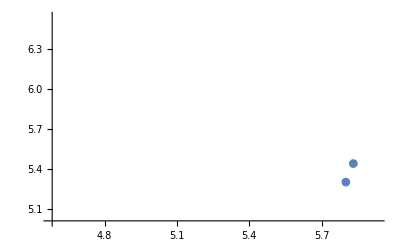
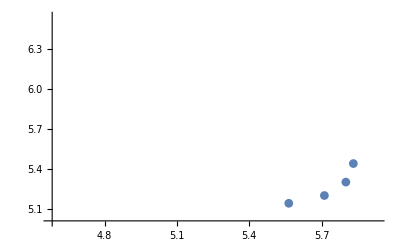
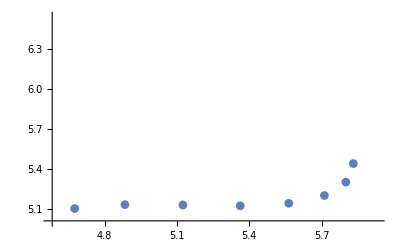
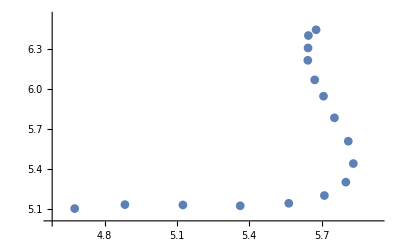

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,1]],PlotMarkers->Automatic,PlotRange->fMaxMins[test]],{i,1,Length@test-1,1}]
```

```mathematica
fMakeArrow[coords__,momenta__]:=Arrow[{coords,coords+momenta}]
fMakeArrowAndPoint[coords__,momenta__,colour_]:=Graphics[{colour,PointSize[Large],Point[coords],fMakeArrow[coords,momenta]}]
fOrderPoints[pts__]:=Module[{segments,edges,path},segments=FindCurvePath@pts;
edges=Partition[#,2,1]&/@segments;
edges=Join@@edges;
path=FindHamiltonianPath@Graph@edges]
fMakeArrowAndPointFirstFinalOnly[coords__,momenta__,colour_]:=Module[{lorder=fOrderPoints[coords],len=Length@coords,coordsordered,momentaordered},coordsordered=coords[[lorder]];momentaordered=momenta[[lorder]];Table[If[Or[i==1,i==len],Graphics[{colour,PointSize[Large],Point[coordsordered[[i]]],fMakeArrow[coordsordered[[i]],momentaordered[[i]]]}],Graphics[{colour,PointSize[Large],Point[coordsordered[[i]]]}]],{i,1,len,1}]]
fConnectFirstLastArrow[coords__,colour_]:=Module[{lorder=fOrderPoints[coords]},Graphics[{colour,Arrow[{coords[[lorder[[1]]]],coords[[lorder[[-1]]]]}]}]]
```

### Make animation

```mathematica
test=fNUTSstring[{5.8,5.3},{0.1,0.2},0.001,0.6,f,1000];
```

```mathematica
fPlotAll[level_Integer,tree_]:=Module[{dep=Depth@tree[[level]][[5]],coordmom,coords,momenta,firstLast,firstLastMomenta},coordmom=If[dep≥ 4, Flatten[tree[[level]][[5]],dep-4],tree[[level]][[5]]];coords=coordmom[[All,1]];momenta=coordmom[[All,2]];firstLast=tree[[level]][[{1,3}]];
firstLastMomenta=tree[[level]][[{2,4}]];If[dep≥4,Show[fMakeArrowAndPointFirstFinalOnly[coords,momenta,Red],Graphics[{Blue,Arrow[firstLast]}]],Graphics[{Red,PointSize[Large],{Black,Point[coordmom[[1]]]},Arrow[{coordmom[[1]],coordmom[[1]]+coordmom[[2]]}]}]]]
```

```mathematica
fCreateAnimations[tree_,gMain_]:=Module[{firstLast=Table[tree[[i]][[{1,3}]],{i,1,Length@tree-1,1}],firstLastMomenta=Table[tree[[i]][[{2,4}]],{i,1,Length@tree-1,1}]},
Table[Show[gMain,fPlotAll[i,tree],PlotRange->{{3,7},{3,7}},PlotLabel->ToString[{(firstLast[[i]][[2]]-firstLast[[i]][[1]]).firstLastMomenta[[i]][[1]],(firstLast[[i]][[2]]-firstLast[[i]][[1]]).firstLastMomenta[[i]][[2]]}]],{i,1,Length@test-1,1}]]
```

```mathematica
ListAnimate[fCreateAnimations[test,gMain]]
```

## Trying more complex density

```mathematica
g[x__]:=Log[PDF[NormalDistribution[5,4],Total[x^2]]]
```

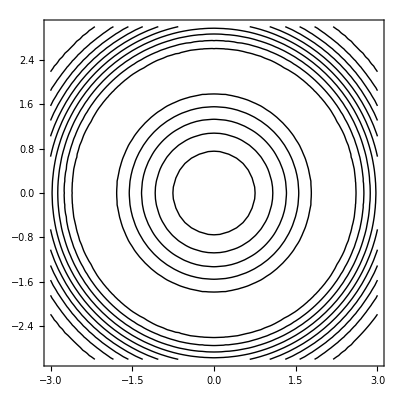

```mathematica
gMain=ContourPlot[Exp[g[{x,y}]],{x,-3,3},{y,-3,3},PlotRange->Full,ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
test=fNUTSstring[{-2,0},{0.4,0.4},1,0.2,g,1000];
```

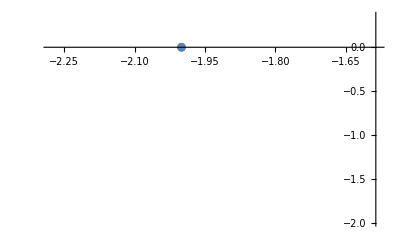
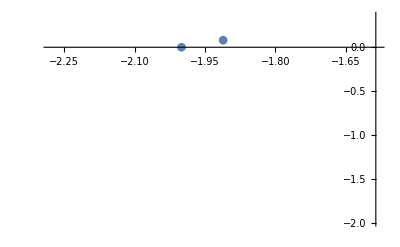
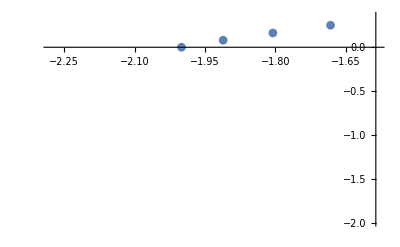
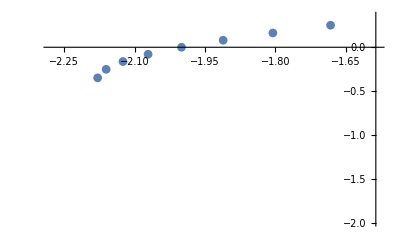
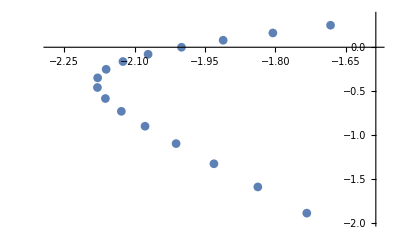

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,1]],PlotMarkers->Automatic,PlotRange->fMaxMins[test]],{i,1,Length@test-1,1}]
```

```mathematica
lAnimations=Table[Show[gMain,Table[ListPlot[fDisjoint[test,1][[i]],PlotRange->fMaxMins[test],PlotStyle->apple13[[i]]],{i,1,j,1}]],{j,1,Length@test-1,1}];
```

```mathematica
ListAnimate[lAnimations]
```

```mathematica
gList=Table[Show[gMain,fPlotAll[i,test],PlotRange->{{-3,3},{-3,3}}],{i,1,Length@test-1,1}];
ListAnimate[gList]
```

## Trying to visualise why NUTS terminates

```mathematica
fIdentifyMinusOrPlusSame[level2nd_Integer,tree_]:=Module[{thetaMinusPlus1=tree[[level2nd-1]][[{1,3}]],thetaMinusPlus2=tree[[level2nd]][[{1,3}]],diff},diff=thetaMinusPlus1-thetaMinusPlus2; diff=Total/@diff;Position[diff,x_/;Abs[x]<0.00000000000001][[1,1]]]
fVectors[level2nd_Integer,tree_]:=Module[{minusPlusSame=fIdentifyMinusOrPlusSame[level2nd,tree],constElement,order,dep=Depth@tree[[level2nd]][[5]],pts,posConst,len,orderedpts,ptsMom},constElement=If[minusPlusSame==1,tree[[level2nd]][[1]],tree[[level2nd]][[3]]];pts=Flatten[tree[[level2nd]][[5]],dep-4][[All,1]];
ptsMom=Flatten[tree[[level2nd]][[5]],dep-4];
len=Length@pts;order=fOrderPoints[pts];
orderedpts=pts[[order]];posConst=Position[orderedpts,constElement][[1,1]];{minusPlusSame,If[posConst==1,ptsMom[[order]],If[posConst==len,Reverse@ptsMom[[order]]]]}]
fReorderVector[minusPlusSame_Integer/;Or[minusPlusSame==1,minusPlusSame==2],ptsMom__]:=If[minusPlusSame==1,ptsMom,Reverse@ptsMom]
fMakeThetaVectors[ptsMom__]:=Module[{pts=ptsMom[[All,1]]},Table[{pts[[1]],pts[[i]]},{i,2,Length@pts,1}]]
fMakeMomentumVectors[ptsMom__]:=Module[{pts=ptsMom[[All,1]],mom=ptsMom[[All,2]]},Table[{{pts[[1]],pts[[1]]+mom[[1]]},{pts[[i]],pts[[i]]+mom[[i]]}},{i,2,Length@pts,1}]]
fMakeMomentumSimple[ptsMom__]:=Module[{mom=ptsMom[[All,2]]},Table[{mom[[1]],mom[[i]]},{i,2,Length@mom,1}]]
fMakeThetaSimple[ptsMom__]:=Module[{pts=ptsMom[[All,1]]},Table[pts[[1]]-pts[[i]],{i,2,Length@pts,1}]]
```

```mathematica
momVecs=fMakeMomentumSimple[fVectors[5,test][[2]]]
```

{{{0.21409,0.167642},{0.304632,0.0882306}},{{0.21409,0.167642},{0.373846,0.0225925}},{{0.21409,0.167642},{0.398234,-0.0073607}},{{0.21409,0.167642},{0.365809,0.010429}},{{0.21409,0.167642},{0.290764,0.0643099}},{{0.21409,0.167642},{0.197081,0.132594}},{{0.21409,0.167642},{0.1,0.2}},{{0.21409,0.167642},{0.00851826,0.255709}},{{0.21409,0.167642},{-0.0653364,0.286141}},{{0.21409,0.167642},{-0.0381529,0.252492}},{{0.21409,0.167642},{-0.0548353,0.216403}},{{0.21409,0.167642},{0.0168683,0.194676}},{{0.21409,0.167642},{0.0390643,0.121084}},{{0.21409,0.167642},{0.0463817,0.115615}},{{0.21409,0.167642},{0.0783003,0.0351914}}}

```mathematica
thetaVecs=fMakeThetaSimple[fVectors[5,test][[2]]]
```

{{-0.157199,-0.0761927},{-0.365558,-0.105877},{-0.605814,-0.103304},{-0.843439,-0.0970439},{-1.04478,-0.115818},{-1.19236,-0.174216},{-1.28128,-0.274932},{-1.31236,-0.414216},{-1.2915,-0.581783},{-1.27827,-0.739326},{-1.24572,-0.884773},{-1.25047,-1.02259},{-1.26596,-1.11839},{-1.28403,-1.21205},{-1.32162,-1.25712}}

```mathematica
#1.#2&@@@Thread[{thetaVecs,momVecs[[All,2]]}]
```

{-0.0546103,-0.139054,-0.240496,-0.30955,-0.311234,-0.258091,-0.183115,-0.117098,-0.0820898,-0.137905,-0.123158,-0.220168,-0.184872,-0.199687,-0.147723}

```mathematica
fNUTSstepSingleString[thetaMinus_,mMinus_,thetaPlus_,mPlus_,C_,j_,s_,u_,ϵ_,logP_,Δ_]:=Module[{thetaMinus1=thetaMinus,mMinus1=mMinus,thetaPlus1=thetaPlus,mPlus1=mPlus,s1=s,temp1,temp2,Cprimed,sprimed,v,C1,j1,dep},
v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus1,mMinus1,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus1,mMinus1,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus1,mPlus1,Cprimed,sprimed}=fBuildTree[thetaPlus1,mPlus,u,v,j,ϵ,logP,Δ]];
dep=Depth@Cprimed-4;
C1=Join[{C},{Cprimed}];
s1=sprimed If[(thetaPlus1-thetaMinus1).mMinus1 ≥ 0,1,0]If[(thetaPlus1-thetaMinus1).mPlus1 ≥ 0,1,0];j1 = j + 1;{thetaMinus1, mMinus1, thetaPlus1, mPlus1,C1,j1,s1,u,ϵ,logP,Δ}]
fUnravel[lTree__]:=Module[{len=Length@lTree,lDeps,lAll},lDeps=Table[Depth@lTree[[i]][[5]],{i,1,len,1}];lAll=Table[Flatten[lTree[[i]][[5]],If[lDeps[[i]]-4>0,lDeps[[i]]-4,0]],{i,1,len,1}];Table[If[i==1,{lAll[[i]]},lAll[[i]]],{i,1,len,1}]]
```

```mathematica
test=fNUTSstring[{5.8,5.3},{0.1,0.2},0.001,0.6,f,1000];
```

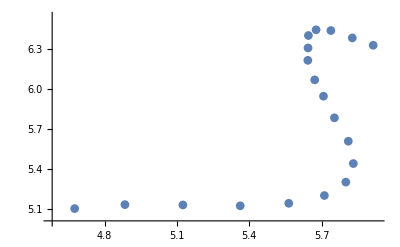
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,1]],PlotMarkers->Automatic,PlotRange->fMaxMins[test]],{i,1,Length@test,1}]
```

```mathematica
sol=fVectors[6,test]
```

{1,{{{4.67592,5.10126},{0.304632,0.0882306}},{{4.88428,5.13095},{0.373846,0.0225925}},{{5.12453,5.12837},{0.398234,-0.0073607}},{{5.36216,5.12211},{0.365809,0.010429}},{{5.5635,5.14089},{0.290764,0.0643099}},{{5.71107,5.19928},{0.197081,0.132594}},{{5.8,5.3},{0.1,0.2}},{{5.83107,5.43928},{0.00851826,0.255709}},{{5.81022,5.60685},{-0.0653364,0.286141}},{{5.75267,5.78265},{-0.106098,0.277257}},{{5.70736,5.94489},{-0.068098,0.237465}},{{5.67095,6.06761},{-0.0428435,0.163065}},{{5.64245,6.21441},{-0.02303,0.199713}},{{5.64332,6.30727},{0.0269571,0.110637}},{{5.64481,6.40062},{0.0278304,0.113716}},{{5.67671,6.44373},{0.0775733,0.0310528}},{{5.7379,6.43789},{0.125016,-0.0509224}},{{5.82673,6.38262},{0.167318,-0.133168}},{{5.9133,6.32743},{0.157211,-0.129952}},{{6.01539,6.22668},{0.170666,-0.196876}},{{6.09071,6.17875},{0.117074,-0.100935}},{{6.15587,6.10556},{0.0901448,-0.133201}},{{6.21504,6.03827},{0.0717582,-0.114115}},{{6.24198,5.96862},{0.0123988,-0.111128}},{{6.29749,5.94104},{0.0564918,-0.0361234}},{{6.30977,5.92527},{-0.0165939,-0.014849}},{{6.32143,5.91046},{-0.0185462,-0.0118172}},{{6.29914,5.89624},{-0.0186896,-0.0119065}},{{6.28752,5.91109},{-0.093631,0.0124231}},{{6.26509,5.8968},{-0.0938895,0.0122316}},{{6.23159,5.89643},{-0.091877,0.00905017}},{{6.15484,5.90766},{-0.159917,0.0231058}}}}

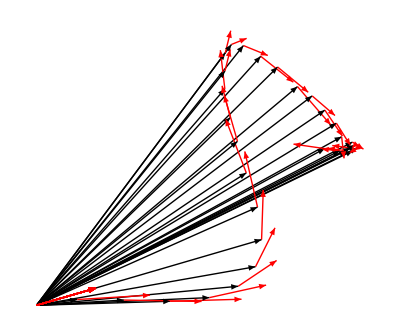

```mathematica
Show[Graphics[Arrow/@fMakeThetaVectors[fReorderVector[sol[[1]],sol[[2]]]]],Show[Graphics[{Red,Arrow/@fMakeMomentumVectors[fReorderVector[sol[[1]],sol[[2]]]][[All,1]]}],Graphics[{Red,Arrow/@fMakeMomentumVectors[fReorderVector[sol[[1]],sol[[2]]]][[All,2]]}]]]
```

```mathematica
momVecs=fMakeMomentumSimple[fVectors[5,test][[2]]]
```

{{{-0.0271751,0.109095},{-0.075048,0.198965}},{{-0.0271751,0.109095},{-0.10701,0.227206}},{{-0.0271751,0.109095},{-0.106098,0.277257}},{{-0.0271751,0.109095},{-0.0653364,0.286141}},{{-0.0271751,0.109095},{0.00851826,0.255709}},{{-0.0271751,0.109095},{0.1,0.2}},{{-0.0271751,0.109095},{0.197081,0.132594}},{{-0.0271751,0.109095},{0.290764,0.0643099}},{{-0.0271751,0.109095},{0.365809,0.010429}},{{-0.0271751,0.109095},{0.398234,-0.0073607}},{{-0.0271751,0.109095},{0.373846,0.0225925}},{{-0.0271751,0.109095},{0.304632,0.0882306}},{{-0.0271751,0.109095},{0.21409,0.167642}},{{-0.0271751,0.109095},{0.118615,0.245018}},{{-0.0271751,0.109095},{0.0298815,0.307577}}}

```mathematica
thetaVecs=fMakeThetaSimple[fVectors[5,test][[2]]]
```

{{-0.0319581,0.092986},{-0.0900575,0.238758},{-0.159823,0.395664},{-0.217375,0.571467},{-0.238226,0.739034},{-0.207153,0.878318},{-0.118226,0.979034},{0.0293446,1.03743},{0.23069,1.05621},{0.468315,1.04995},{0.708572,1.04737},{0.916931,1.07706},{1.07413,1.15325},{1.17384,1.27823},{1.21647,1.44727}}

```mathematica
#1.#2&@@@Thread[{thetaVecs,momVecs[[All,2]]}]
```

{0.0208994,0.0638845,0.126658,0.177723,0.186948,0.154948,0.106514,0.0752495,0.0954037,0.178771,0.288559,0.374355,0.423294,0.452424,0.481497}